```mathematica
ClearAll["Global`*"]
```

The beta function evolution equation reduces to a Cauchy-Euler equation if the matched beta function is expanded to first order. Solving the third order CE equation requires solving the cubic equation:

```mathematica
Solve[α^3 m (m-1) (m-2)+α m-α==0,m]
```

{{m→1},{m→(α^2-√(-α^2+α^4))/α^2},{m→(α^2+√(-α^2+α^4))/α^2}}

Using these values of m the solution is given by

```mathematica
βm[s_]=βm0-2 α (s-s0);
Φ[s_]=Log[βm[s]] √(1-α^2)/α;
β[s_]=βm[s] (c0+A Cos[Φ[s]+Φ0]);
```

To find the unknown coefficient c0 this solution is plugged back into the original differential equation.

```mathematica
Simplify[1/2 β''[s]+1/βm[s]^2 β[s]-1/β[s] (1+(β'[s]/2)^2)]
```

((-A^2+c1^2+c2^2) (-1+α^2))/((-1+2 s α) (√(c1^2+c2^2+1/(1-α^2))+A Cos[Φ0+(√(1-α^2) Log[1-2 s α])/α]))

```mathematica
c0=√(A^2+1/(1-α^2));
```

The negative square root is dropped because if A is very large the only way for β to stay positive is for if c0 is positive. 

It ends up that form of the solution is hard to solve for the coefficients but we can use the version below and solve for them easily.

```mathematica
c0=√(c1^2+c2^2+1/(1-α^2));
β[s_]=βm[s] (c0+c1 Cos[Φ[s]]+c2 Sin[Φ[s]]);
s0=0;
βm0=1;
initCont=Solve[{β[0]==β0,β'[0]==-2 α0},{c1,c2}];
FullSimplify[c1/.initCont]
FullSimplify[c2/.initCont]
```

{(1+α0^2-2 α α0 β0+(-1+2 α^2) β0^2)/(2 (-1+α^2) β0)}

{(α0-α β0)/(√(1-α^2))}

Using these we can solve for the case where the beam begins matched and propagates through the plasma for different values of α_m.

```mathematica
init={α0->0,β0->1};
FullSimplify[c1/.initCont/.init]
FullSimplify[c2/.initCont/.init]
FullSimplify[c0/.initCont/.init]
```

{α^2/(-1+α^2)}

{-α/(√(1-α^2))}

{√(1/((-1+α^2)^2))}

The vacuum waist can be solved for assuming the plasma ends a distance l from the top of the ramp.

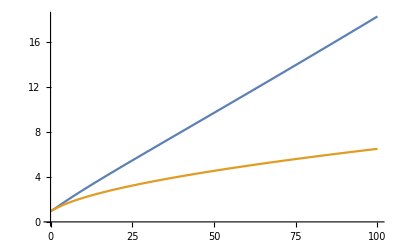

```mathematica
βmat[s_]=(1-2 α s) (1+α^2/(1-α^2) (1-Cos[Φ[s]])-α/(√(1-α^2)) Sin[Φ[s]]);
Plot[{βmat[s]/(βmat'[s]^2/4+1)/.α->-0.9,βmat[s]/(βmat'[s]^2/4+1)/.α->-1.1},{s,0,100}]
```